## A single p-bit

The sigmoid plot shows a single p-bit’s probability of being in a ‘+1’ state as a function of the input I_i and the temperature T.

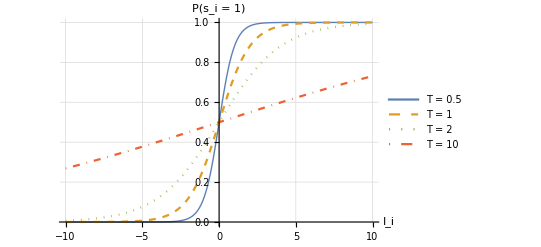

```mathematica
(*Define the p-bit probability function*)
P[Ii_,T_]:=1/(1+Exp[-Ii/T])

(*Plot the function for four different values of T*)
Plot[{P[Ii,0.5],P[Ii,1],P[Ii,2],P[Ii,10]},{Ii,-10,10},PlotLegends->Placed[{"T = 0.5","T = 1","T = 2","T = 10"},{0.8,0.3}],PlotRange->{0,1},AxesLabel->{"I_i","P(s_i = 1)"},PlotStyle->{Thick,Dashed,Dotted,DotDashed},GridLines->Automatic]
```

## Coupling 2 p-bits together

This graph visually shows 2 p-bits coupled together by some weight J_12. Each bit is in a +1 or -1 state at any given time.

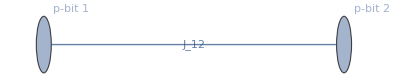

```mathematica
g=Graph[{2<->1},(*Define an undirected edge between node 1 and node 2*)VertexLabels->{1->"p-bit 1",2->"p-bit 2"},(*Label the vertices*)
VertexSize->0.05,
EdgeLabels->{1<->2->"J_12"}(*Label the coupling strength*)
];

(*Display the graph*)
g
```

This code simulates 2 p-bits connected by a weight J, with biases h1 and h2, at constant temperature T. The output is the frequency with which we measure each of 4 possible system states/spin configurations, represented as a probability.

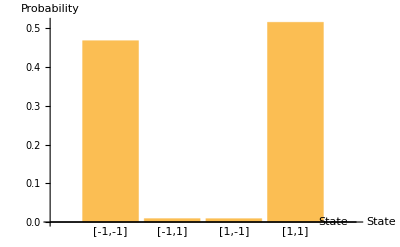

```mathematica
(*Parameters*)
(*You can and should play with different values of J and T. T is always > 0. J can be positive, negative, or 0 if the bits are not coupled at all. *)
J=1;(*If the coupling between the 2 p-bits is positive, it encourages them to align in the same direction *)
h1=0;                    (*Bias to p-bit #1*)
h2=0;                    (*Bias to p-bit #2*)
T=1;                     (*Absolute temperature*)

(*Energy function using the Ising model,where m and n are the states of the two p-bits*)
Energy[m_,n_]:=-(J m n+h1 m+h2 n)

(*Activation function for bipolar p-bits using tanh-based expression*)
activation[I_,T_]:=Sign[Tanh[I/T]-(2*RandomReal[{0,1}]-1)]

(*Initial random states for the two p-bits using bipolar values+1 or-1*)
m=Sign[2*RandomReal[{0,1}]-1];
n=Sign[2*RandomReal[{0,1}]-1];

(*Perform Gibbs sampling:take 10000 samples*)
samples=First@Last@Reap@Do[(*Update p-bit #1 based on the current state of p-bit #2*)I1=-(Energy[1,n]-Energy[-1,n]);
m=activation[I1,T];
(*Update p-bit #2 based on the new state of p-bit #1*)I2=-(Energy[m,1]-Energy[m,-1]);
n=activation[I2,T];
(*Store the combined state as a list {m,n}*)Sow[{m,n}],10000];

(*Map the states to their corresponding labels*)
labeledSamples=samples/. {{-1,-1}->"[-1,-1]",{-1,1}->"[-1,1]",{1,-1}->"[1,-1]",{1,1}->"[1,1]"};

(*Count the frequency of each state*)
counts=Tally[labeledSamples];

(*Sort by the label to ensure proper order*)
sortedCounts=SortBy[counts,First];

(*Extract the labels and corresponding frequencies*)
labels=sortedCounts[[All,1]];
frequencies=sortedCounts[[All,2]];

(*Convert frequencies to probabilities*)
probabilities=N[frequencies]/Total[frequencies];

(*Create a bar chart with labeled bins*)
BarChart[probabilities,ChartLabels->Placed[labels,Below],AxesLabel->{"State","Probability"}]
```

## A system of 4 p-bits

The following code simulates a system of 4 p-bits. It outputs a histogram showing the frequency with which we measure each energy state, expressed as a probability.

-Graphics-

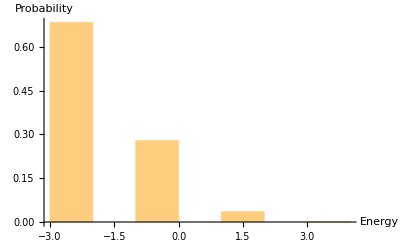

```mathematica
(*Parameters*)
nBits=4;  (*Number of p-bits in the system*)

(*Adjacency matrix for coupling between p-bits (J_ij)*)
(*You can edit the adjacency matrix and play with the weights. Make sure it is symmetric, and J_ij = J_ji*)
J={{0,1,0,0},{1,0,1,0},{0,1,0,1},{0,0,1,0}};

(*Create an adjacency graph with labels*)graph=AdjacencyGraph[J,VertexLabels->"Name",(*Label the vertices with their numbers*)EdgeLabels->EdgeWeight]; (*Label the edges with their weights*)

(*Display the graph*)
Graph[graph,VertexLabels->Placed["Name",Center],EdgeLabels->Placed["EdgeWeight",Center],GraphStyle->"SpringElectricalEmbedding", VertexSize->0.1]

(*Bias vector (h_i)*)
h={0,0,0,0};

T=1;  (*Absolute temperature*)

(*Activation function for bipolar p-bits using tanh-based expression*)
activation[input_,temp_]:=Sign[Tanh[input/temp]-(2*RandomReal[{0,1}]-1)]

(*Initial random states for the 4 p-bits using bipolar values+1 or-1*)
states=Sign[2*RandomReal[{0,1},nBits]-1];

IsingHamiltonian[state_List]:=-0.5*Sum[J[[i,j]]*state[[i]]*state[[j]],{i,1,nBits},{j,1,nBits}]-Sum[h[[i]]*state[[i]],{i,1,nBits}];

(*Perform Gibbs sampling:take 10000 samples*)
samples=First@Last@Reap@Do[(*Update each p-bit sequentially*)For[k=1,k<=nBits,k++,(*Calculate the input for the activation function*)input=Sum[J[[k,j]]*states[[j]],{j,1,nBits}]+h[[k]];
(*Update the state of the k-th p-bit*)states[[k]]=activation[input,T];];
(*Store the current state*)Sow[states],{sweep,10000}];

(*Map the sampled states to Ising Hamiltonian values*)
hamiltonians=IsingHamiltonian/@samples;

(*Plot histogram of the Ising Hamiltonian values*)
Histogram[hamiltonians,{1},"Probability",ChartLabels->None,(*Remove the ChartLabels to avoid the overlap*)LabelStyle->{FontSize->14},AxesLabel->{"Energy","Probability"}]
```

The following code calculates the Boltzmann distribution analytically. It calculates the energy of each possible spin configuration (2^N possibilities, where N is the number of p-bits in the system). It then applies P({m}) = 1/Z exp(-E{m}/T), where P(E{m}) is the probability of observing a particular energy corresponding to the spin state {m}, and Z is the partition function (a normalization constant). Note that multiple different spin configurations could have the same energy E; we call these degenerate states. We must account for this: two different states with the same energy E have their own probability P(E{m}).

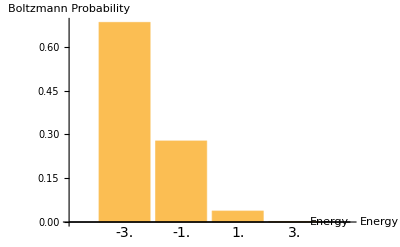

```mathematica
(*Parameters*)
nBits=4;  (*Number of p-bits in the system*)

(*Adjacency matrix for coupling between p-bits (J_ij)*)
(*You can edit the adjacency matrix and play with the weights. Make sure it is symmetric, and J_ij = J_ji*)
J={{0,1,0,0},{1,0,1,0},{0,1,0,1},{0,0,1,0}};

(*Bias vector (h_i)*)
h={0,0,0,0};

T=1;  (*Absolute temperature*)

(*Calculate all possible states for nBits=4*)
allStates=Tuples[{-1,1},nBits];

(*Calculate the energy of each possible state*)
energies=IsingHamiltonian/@allStates;

(*Identify unique energies and their degeneracies*)
uniqueEnergiesWithDegeneracy=Tally[energies];

(*Calculate Boltzmann weights for each unique energy level,accounting for degeneracy*)
boltzmannWeightsWithDegeneracy=Exp[-#[[1]]/T] #[[2]]&/@uniqueEnergiesWithDegeneracy;

(*Normalize the Boltzmann weights*)
Z=Total[boltzmannWeightsWithDegeneracy];
normalizedBoltzmannHistogram=boltzmannWeightsWithDegeneracy/Z;

(*Plot the Boltzmann distribution*)
BarChart[normalizedBoltzmannHistogram,ChartLabels->Placed[uniqueEnergiesWithDegeneracy[[All,1]],Below],LabelStyle->{FontSize->14},AxesLabel->{"Energy","Boltzmann Probability"}]
```